## Training a classifier for source attribution of campylobacteriosis

Campylobacter is a foodborne pathogen that is the largest  cause  of bacterial gastroenteritis in the developed world.

Campylobacter is a zoonotic pathogen hosted by several animals including cattle, chicken, sheep, pig or wild birds. Food products from these animals represent a risk of infection to humans which can develop campylobacteriosis. If someone is infected, it is important to determine the origin of infection, i.e. which type of food is responsible for the transmission to the infected patient. If the source is identified, the authorities may decide to call back certain foods from the market to prevent further infections.

The aim of this practical is to use genomic data for Campylobacter samples from five animal reservoirs (see Figure) to train a classifier so that infections in humans can be attributed to one of the five reservoirs. The ultimate goal is to use the classifier to determine the origin of Campylobacter samples isolated from infected humans. In the dataset to be used, each sample is characterised by seven housekeeping genes for Campylobacter. Each gene is coded by a set of numbers (alleles). In practice, each sample is characterised by a feature vector consisting of 7 integer numbers. 

The dataset contains Campylobacter samples isolated from humans and from animal reservoirs (cattle, chicken, sheep, pig and wild bird).  You will first deal with samples from animal reservoirs to train a classifier and test its performance. After that, you will be ready to attribute human isolates to food sources. 

Practical suggestions:

Make sure that you understand the analysis of the Iris flowers done in lectures before attempting this practical!

Names for new variables are normally suggested throughout the practical. This is done to be able to refer to such variables in forthcoming tasks of the practical. You are free to use other names but this might be confusing. In addition, the solutions to the practical provided later will use the suggested names and you might find useful to use the same names to compare.

-Graphics-
Image from Francisco J.Pérez-Reche,Ovidiu Rotariu,Bruno S.Lopes,Ken J.Forbes and Norval J.C.Strachan "Mining Whole Genome Sequence data to efficiently attribute individuals to source populations" (2019).

#### These answers are split into two sections which present slightly different ways to address the questions. The first section probably uses simpler Mathematica functions (for instance, option 1 uses simple Import and option 2 uses SemanticImport). Both ways to answer the questions are fine and both would have obtained full marks if the practical would assessed (it is not). The second section looks at the bias problem as well.

## Option 1: Training A Classifier Function

## Task 1

Download the dataset Campylobacter_MLST.csv from MyAberdeen

Import the data and assign it to a variable (e.g. data)

### Answer

These are the commands I used to load the data in my computers. The command depends on whether I use a Windows or Linux machine.

```mathematica
(*Paco's import*)
data=Import["~/Teaching/MSc_Data_Science/Data/Campylobacter/Campylobacter_MLST.csv"];
```

```mathematica
(*Luke's import*)
SetDirectory[NotebookDirectory[]]
data=Import["Campylobacter_MLST.csv"];
```

/home/paco/Teaching/MSc_Data_Science/2020-2021/Practicals

Import::nffil: File Campylobacter_MLST.csv not found during Import.

```mathematica
data
```

{{Cattle,2,1,5,3,725,1,5},{Cattle,1,2,3,4,5,9,3},{Cattle,19,24,23,20,26,16,15},{Cattle,2,1,1,3,2,1,5},{Cattle,1,4,2,2,6,3,17},{Cattle,9,2,4,62,4,5,6},{Cattle,1,1,59,2,10,5,7},1160,{Human,9,2,4,62,4,5,6},{Human,33,39,30,82,104,56,17},{Human,4,7,40,4,42,51,1},{Human,2,1,12,3,2,1,5},{Human,4,7,10,4,1,7,1},{Human,4,7,10,4,42,51,1}}
 |  |  |  |

## Task 2

Examine the format of the dataset. For instance, use the function Take to see the 10 first instances and look at the dimensions of the dataset. As you will see, data is a list of lists. It can be thought as a table consisting of 8 columns and 1173 rows. The first column gives the category of each isolate and each row corresponds to a different isolate.

### Answer

```mathematica
Take[data,10]
```

{{Cattle,2,1,5,3,725,1,5},{Cattle,1,2,3,4,5,9,3},{Cattle,19,24,23,20,26,16,15},{Cattle,2,1,1,3,2,1,5},{Cattle,1,4,2,2,6,3,17},{Cattle,9,2,4,62,4,5,6},{Cattle,1,1,59,2,10,5,7},{Cattle,1,462,2,2,6,3,17},{Cattle,2,1,5,3,2,1,5},{Cattle,1,3,6,4,3,3,3}}

The number of rows is

```mathematica
Length[data]
```

1173

and the number of columns is

```mathematica
Length[data[[1]]]
```

8

## Task 3

Look at the name of different categories in the dataset which are given in the first column for each instance (isolate). This can be done by DeleteDuplicates.

### Answer

```mathematica
DeleteDuplicates[data[[All,1]]]
```

{Cattle,Sheep,Chicken,Pig,WB,Human}

## Task 4

Since the isolates from food reservoirs are assumed to be the sources of human isolates, it makes sense to split the list data into two lists, one corresponding to human isolates and another for isolates from food reservoirs.  The resulting lists should have the same format (e.g. same number of columns) as data. More explicitly:

Create a sublist from data for human isolates. Refer to it as dataHuman.

Create a list containing the data for food reservoirs only. Refer to the new list as dataSources.

As usual when defining new lists or variables, check that they look like you expect them to look.

### Answer

```mathematica
dataHuman=data[[Flatten[Position[data[[All,1]],"Human"]]]];
```

```mathematica
dataHuman;
```

```mathematica
Flatten[Position[data[[All,1]],"Human"]];
```

```mathematica
Table[i,{i,1,Length[data]}];
```

```mathematica
dataSources=data[[Complement[Table[i,{i,1,Length[data]}],Flatten[Position[data[[All,1]],"Human"]]]]];
```

```mathematica
Length[dataHuman]
```

500

```mathematica
Length[dataSources]
```

673

## Task 5

Use dataSources to define a list named sourcenames containing the name of the sources. This will be useful to explore the data below. Note that isolates from wild birds are labeled as WB.

### Answer

```mathematica
sourcenames=DeleteDuplicates[dataSources[[All,1]]]
```

{Cattle,Sheep,Chicken,Pig,WB}

## Task 6

In the forthcoming analysis, it will be useful to have a list with the name of features (genes). For the purposes of this practical, you can refer to the genes as “gene 1”, “gene 2”,... “gene 7”

```mathematica
featurename={"gene 1","gene 2","gene 3","gene 4","gene 5","gene 6","gene 7"}
```

{gene 1,gene 2,gene 3,gene 4,gene 5,gene 6,gene 7}

## Task 7

Separate the instances in dataSources by source. In order to achieve this task, you may want to go back to the Iris flowers classification example where a similar task was done.

### Answer

As explained in the Iris flowers classification problem, there are at least two ways to achieve this: by using Cases or Position. Both should give the same result.

```mathematica
bySources=Cases[dataSources,{#,___}]&/@sourcenames;
```

```mathematica
bySources=Table[dataSources[[Flatten[Position[dataSources,sourcenames[[i]]]]]],{i,1,Length[sourcenames]}];
```

## Task 8

The goal of the classifier to be trained in this practical will be to classify unseen isolates into food reservoirs. In order for classification to be accurate, we need a reasonable separation between different reservoirs in the feature space. The feature space in this case consists of 7 dimensions (each isolate is represented by a point in this space and its coordinates are the values taken by its 7 genes). 

Since the dimension of the feature space is larger than 3, it is difficult to visualise at once on a 2D screen. 

One possible way to do a preliminary exploration is to plot the alleles for pairs of genes (pairs of features) and pairs of sources. This can be done using the following scatterplot:

```mathematica
bySources[[1]][[1]]
```

{Cattle,2,1,5,3,725,1,5}

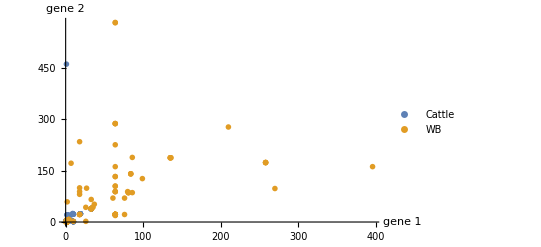

```mathematica
f1=1;
f2=2;
source1=1;
source2=5;
ListPlot[{bySources[[source1]][[All,{f1+1,f2+1}]],bySources[[source2]][[All,{f1+1,f2+1}]]},AxesLabel->featurename[[{f1,f2}]],PlotLegends->sourcenames[[{source1,source2}]],PlotMarkers->{"OpenMarkers", Medium},PlotRange->All]
```

Here, f1 and f2 correspond to features (genes). source1 and source2 correspond to two reservoirs.

In order to compare pairs of reservoirs, I suggest you proceed as follows:

Make sure you understand how the plot is made.

Systematically compare the scatterplot for pairs of sources and pairs of genes. The comparison between sources in this case is not as clear as the comparison between species in the Iris flowers problem. However, we can extract some preliminary conclusions. Which sources do you think are more different from each other? These are the ones that the classifier you will train later should identify more accurately.

### Answer

Although it is not easy to identify clear trends in the data, one can observe the following:

WB isolates are the ones that cover a larger part of the feature space. They seem to be quite different to other isolates.

Pig isolates also cover a large region in the feature space and do not overlap much with other sources.

The point clouds for cattle and sheep seem to overlap more than those for any other sources.

The point clouds for chicken does not spread over a region as wide as pig and WB but they seem to be reasonably separated from the clouds of other sources.

You may find useful to use a scatterplot with dynamical ranges as follows (make sure you understand how this is built):

```mathematica
f1=1;
f2=2;
Manipulate[ListPlot[Table[bySources[[i]][[All,{f1+1,f2+1}]],{i,1,Length[sourcenames]}],PlotLegends->sourcenames,PlotMarkers->{"OpenMarkers", Medium},PlotRange->{{0,x},{0,y}}],{x,10,800},{y,10,800}]
```

## Task 9

In order to further analyse the data and try to confirm some of your conclusions in the previous task, plot a scatter plot matrix. In order to reduce the complexity of the scatter plot matrix, you may want to plot a reduced number of features (genes) at once.

### Answer

One can define a function to do scatter plot matrix plots automatically. The inputs for the function are as follows:

values: matrix with values for all features
names: names of the features
vfeatures: vector with the feature number to be plotted 
vclass: vector with class of each instance

```mathematica
ScatterPlotMatrix[values0_,names0_,vfeatures0_,vclass0_]:=Module[{values=values0,names=names0,vf=vfeatures0,vc=vclass0,classes,pos},
classes=DeleteDuplicates[vc];
pos=Table[Flatten[Position[vc,classes[[i]]]],{i,1,Length[classes]}];
Table[If[i==j,names[[i]],ListPlot[Table[Transpose[{values[[pos[[ic]],i]],values[[pos[[ic]],j]]}],{ic,1,Length[classes]}],PlotMarkers->{"OpenMarkers", Small},PlotLegends->DeleteDuplicates[vclass0],PlotRange->All]],{i,vf},{j,vf}]//Grid
]
```

Dissecting the function to see how it works:

```mathematica
vc=dataSources[[All,1]];
classes=DeleteDuplicates[vc];
```

```mathematica
classes
```

{Cattle,Sheep,Chicken,Pig,WB}

```mathematica
pos=Table[Flatten[Position[vc,classes[[i]]]],{i,1,Length[classes]}];
```

```mathematica
pos
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150},{151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300},{301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450},{451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580},{581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673}}

```mathematica
Flatten[Position[vc,classes[[2]]]]
```

{151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300}

```mathematica
pos
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150},{151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300},{301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450},{451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580},{581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673}}

For instance, the scatter plots for the first three genes look like:

```mathematica
dataSources[[All,2;;8]]
```

{{2,1,5,3,725,1,5},{1,2,3,4,5,9,3},{19,24,23,20,26,16,15},{2,1,1,3,2,1,5},{1,4,2,2,6,3,17},{9,2,4,62,4,5,6},{1,1,59,2,10,5,7},{1,462,2,2,6,3,17},{2,1,5,3,2,1,5},{1,3,6,4,3,3,3},{2,4,2,2,6,1,5},{2,1,12,88,2,1,5},{2,1,1,3,2,1,5},{1,4,2,2,6,3,17},{10,1,59,19,10,5,7},{33,39,30,82,104,56,17},{19,24,23,20,26,16,15},{2,1,1,3,2,1,5},{1,2,3,4,5,9,3},{1,1,59,2,10,5,7},{1,4,2,2,6,3,17},{9,2,4,62,4,5,6},{2,4,1,2,7,1,5},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{10,23,16,19,6,18,7},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{33,39,30,82,104,56,17},{9,2,4,62,4,5,6},{19,24,23,20,26,16,15},{2,4,1,2,7,1,5},{9,25,2,10,22,3,6},{33,39,30,82,104,56,17},{9,2,4,62,4,5,6},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{2,1,1,3,2,1,5},{2,4,2,2,6,1,5},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{2,21,5,37,2,1,5},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{2,4,1,2,7,1,5},{1,2,3,4,5,9,3},{1,4,2,2,6,3,17},{9,2,4,62,4,5,6},{4,7,10,4,42,7,1},{1,4,2,2,6,3,17},{2,1,5,3,2,1,5},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{2,21,5,37,2,1,5},{1,4,2,2,6,3,17},{9,2,4,62,4,5,6},{1,1,59,2,10,5,7},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{10,1,59,19,10,5,7},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{10,23,16,19,6,18,332},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{10,1,59,19,10,5,7},{1,3,6,4,3,3,3},{2,1,1,3,2,1,5},{1,2,3,4,5,9,3},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{7,21,5,62,4,61,44},{2,1,12,3,2,1,5},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{2,1,5,3,2,1,5},{10,23,16,19,6,18,7},{2,1,5,10,2,1,5},{2,4,2,2,6,1,5},{2,1,1,3,2,1,5},{19,24,23,20,26,16,15},{19,24,42,246,300,259,57},{1,3,6,4,3,3,3},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{1,1,59,2,10,5,7},{2,1,5,3,2,54,5},{2,4,2,2,6,1,5},{2,1,5,3,725,1,5},{2,1,5,3,2,1,5},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{1,2,3,4,5,9,3},{10,1,59,19,10,5,7},{1,1,59,2,10,5,7},{1,2,3,4,5,9,3},{2,21,5,37,2,1,5},{19,24,23,20,26,16,15},{7,21,5,62,4,61,44},{33,39,30,82,104,56,17},{2,1,1,3,2,1,5},{2,1,1,3,2,1,5},{1,4,250,2,6,3,17},{1,3,6,4,3,3,3},{19,24,23,20,26,16,15},{1,2,3,4,5,9,3},{1,2,3,4,5,9,3},{1,2,3,4,5,9,3},{33,39,30,82,104,56,17},{2,4,2,2,6,1,5},{2,21,5,37,2,1,5},{33,39,30,82,104,56,17},{10,1,59,19,10,5,7},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{1,4,2,2,710,259,17},{2,1,1,3,2,1,5},{2,1,5,3,2,1,5},{2,21,5,2,60,1,5},{2,1,5,3,2,1,5},{2,1,5,3,2,1,5},{1,4,2,2,6,3,17},{2,4,1,2,7,1,5},{19,24,23,20,26,16,15},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{10,23,16,19,6,18,7},{2,1,5,3,2,1,5},{2,1,1,3,2,1,5},{9,2,4,62,4,5,6},{1,4,2,2,6,3,17},{2,1,5,3,2,1,5},{2,1,5,3,2,1,5},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{2,21,5,2,60,1,5},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{2,1,5,3,2,1,5},{33,39,30,82,113,47,17},{33,39,30,82,104,56,17},{19,24,23,20,26,16,15},{1,4,2,2,6,1,17},{2,1,5,3,2,1,5},{2,1,12,88,2,1,5},{10,27,43,19,6,18,7},{2,1,5,3,2,1,5},{33,39,30,82,104,47,36},{2,1,1,3,2,1,5},{2,1,1,3,2,1,3},{1,2,3,4,5,9,3},{33,39,30,82,113,47,17},{33,39,30,82,113,47,17},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{33,39,30,82,104,47,36},{33,39,30,82,113,47,17},{1,2,3,4,5,9,3},{2,1,1,3,2,1,5},{33,39,30,82,113,47,17},{33,39,30,82,104,56,17},{33,39,30,82,113,47,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{2,1,1,3,2,1,5},{2,1,1,3,2,1,3},{2,1,1,3,2,1,5},{2,1,1,3,2,1,5},{9,2,4,62,4,5,6},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{2,1,5,3,2,1,5},{33,39,30,82,104,47,17},{2,1,1,3,2,1,3},{53,38,30,81,118,71,36},{2,1,5,3,2,1,5},{33,39,30,82,113,47,17},{2,1,5,3,2,1,5},{7,21,5,62,4,61,44},{2,1,5,3,2,1,5},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{33,39,30,82,104,47,36},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{2,4,1,2,7,1,5},{2,1,1,3,2,1,3},{53,38,30,81,118,71,36},{1,3,6,4,3,3,3},{1,4,2,2,6,3,17},{33,39,30,82,113,47,17},{2,1,1,3,2,1,5},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{1,4,2,2,6,1,17},{33,39,30,82,104,56,17},{33,39,30,82,113,44,17},{1,4,2,2,6,3,17},{33,39,30,82,113,47,17},{33,39,30,82,104,56,17},{33,39,30,82,113,47,17},{2,1,5,3,2,1,5},{2,1,21,3,2,1,5},{33,39,30,82,113,47,17},{2,1,5,3,2,1,5},{2,4,1,2,7,1,5},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{2,1,1,3,2,1,3},{33,39,30,82,104,47,36},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{2,1,5,3,2,1,5},{2,21,5,2,60,1,5},{33,39,30,82,113,44,17},{2,1,5,3,2,1,5},{1,4,2,2,6,1,17},{2,1,1,3,2,1,3},{1,4,2,2,6,3,17},{33,39,30,82,113,47,17},{2,1,1,3,2,1,5},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{33,39,30,82,104,56,17},{2,1,1,3,2,1,3},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{2,21,5,2,60,1,5},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{2,1,1,3,2,1,5},{1,1,2,2,6,3,17},{19,24,23,20,26,16,15},{2,1,1,3,2,1,5},{2,21,5,37,60,1,5},{2,1,1,560,2,1,5},{2,21,5,37,2,1,5},{2,4,1,2,7,1,5},{2,1,5,3,2,1,5},{2,1,1,3,2,1,5},{2,1,1,3,2,1,3},{53,38,30,81,118,71,36},{2,21,5,2,60,1,5},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{2,1,1,3,2,1,3},{1,4,2,2,6,3,17},{33,39,30,82,711,56,17},{1,4,2,2,6,3,17},{2,1,1,3,2,1,3},{2,1,1,3,2,1,5},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{2,1,21,3,2,1,5},{2,1,12,88,2,1,5},{1,4,2,2,6,3,17},{2,21,5,37,2,1,5},{2,1,21,3,2,1,5},{4,7,10,4,1,7,1},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{33,39,30,82,104,47,36},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{2,21,5,37,60,1,5},{2,1,1,3,2,1,5},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{2,1,12,88,2,1,5},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{2,1,21,3,2,1,5},{2,21,5,37,2,1,5},{2,21,5,37,2,1,5},{1,4,2,2,6,3,17},{2,1,1,3,2,1,5},{2,21,5,37,2,1,5},{2,1,1,560,2,1,5},{9,2,4,62,4,5,12},{2,1,12,3,2,1,5},{7,17,2,3,23,3,12},{2,1,12,3,2,1,5},{7,17,2,15,23,3,12},{9,2,4,62,4,5,6},{2,4,2,4,19,3,6},{4,7,10,4,1,7,1},{9,2,4,62,4,5,6},{2,1,5,3,2,1,5},{4,7,10,4,1,7,1},{9,2,4,62,4,5,12},{33,38,30,82,118,43,17},{7,17,2,15,23,3,12},{9,2,4,62,4,5,12},{2,1,12,3,2,1,5},{33,38,30,173,104,35,68},{24,2,2,2,10,3,3},{1,2,42,4,3,40,3},{2,4,1,2,7,1,5},{2,4,1,2,7,1,5},{33,38,30,82,104,43,388},{104,7,10,4,1,7,1},{2,1,12,3,2,1,5},{2,4,1,2,7,1,5},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{7,17,2,15,23,3,12},{2,1,12,3,2,1,5},{9,2,4,62,4,5,6},{2,1,1,3,2,1,5},{9,25,2,10,22,3,6},{7,53,2,10,11,3,3},{9,2,4,62,4,5,6},{14,17,5,2,11,3,6},{9,17,52,10,10,3,1},{2,4,1,2,7,1,5},{2,1,21,3,2,1,5},{4,7,40,4,42,51,1},{33,39,30,82,113,47,17},{9,17,5,10,350,3,3},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{2,1,12,3,2,1,5},{24,2,2,2,10,3,3},{2,4,1,2,7,1,5},{9,2,4,62,4,133,6},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{4,7,10,4,42,25,1},{24,2,2,2,10,3,3},{2,4,1,2,7,1,5},{24,2,2,2,10,3,3},{2,10,2,4,19,3,6},{9,2,4,62,4,5,6},{2,1,21,3,2,1,5},{4,7,10,4,1,7,1},{1,2,42,4,3,40,3},{2,1,12,3,2,1,5},{4,7,10,4,42,7,1},{4,7,10,4,1,7,1},{33,39,30,82,104,56,17},{9,2,4,62,4,5,12},{7,17,2,15,23,3,12},{2,1,12,3,2,1,5},{9,2,4,62,4,5,6},{24,2,2,2,10,3,3},{2,4,1,2,7,1,5},{7,17,2,15,23,3,12},{33,39,30,82,113,47,17},{4,7,10,4,42,51,1},{9,2,4,62,4,5,6},{8,10,2,2,11,12,6},{2,4,1,2,7,1,5},{4,7,10,4,1,7,1},{8,10,2,2,11,12,6},{6,4,5,2,2,1,5},{2,1,1,3,2,1,5},{24,2,2,2,10,3,3},{8,10,2,2,11,12,6},{6,4,5,2,2,1,5},{24,2,2,2,10,3,3},{24,2,2,2,10,3,3},{2,75,4,48,141,34,1},{24,2,2,2,10,3,3},{2,4,1,2,7,1,5},{24,2,2,2,10,3,3},{2,1,1,3,2,1,5},{24,2,2,2,10,3,3},{1,4,2,2,6,3,17},{24,2,2,2,10,3,3},{2,1,12,3,2,1,5},{2,1,5,3,2,1,5},{7,17,2,15,23,3,12},{2,115,57,26,127,29,35},{7,17,2,15,23,3,12},{24,2,2,2,10,3,3},{24,2,2,2,10,3,3},{2,1,21,3,2,1,5},{4,7,10,4,42,51,1},{2,1,12,3,2,1,5},{9,2,4,62,4,5,6},{9,2,4,62,4,5,6},{7,17,2,15,23,3,12},{7,28,4,28,17,34,12},{2,1,12,3,2,1,5},{9,2,4,62,4,5,6},{2,4,1,2,7,1,5},{2,1,1,3,2,1,3},{7,17,2,15,23,3,12},{2,4,1,2,7,1,5},{9,2,4,62,4,5,6},{2,4,1,2,7,1,5},{24,2,2,2,10,3,1},{7,17,2,3,23,3,12},{32,38,30,82,113,43,17},{7,17,2,15,23,3,12},{2,1,12,3,2,1,5},{7,17,2,15,23,3,12},{6,4,5,2,2,1,5},{2,4,1,93,11,3,6},{2,1,12,3,2,1,5},{2,1,12,3,2,1,5},{7,4,2,2,11,3,5},{4,7,10,4,42,51,1},{2,1,5,3,2,1,5},{4,7,10,4,1,7,1},{7,17,2,15,23,3,12},{4,7,10,4,1,7,1},{104,7,10,4,1,7,1},{4,7,40,4,42,51,1},{37,365,21,64,505,24,23},{2,1,12,3,2,1,5},{2,1,12,88,2,1,5},{24,2,2,2,10,3,3},{2,1,21,334,2,1,5},{7,17,2,15,23,3,12},{2,4,1,2,7,1,5},{4,7,10,4,42,51,1},{9,2,4,62,4,5,12},{2,1,5,3,2,1,5},{4,7,10,4,42,51,1},{2,4,1,2,7,1,5},{33,39,30,79,104,47,17},{76,22,72,98,116,518,16},{2,4,1,2,7,1,5},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{4,7,10,4,1,7,1},{4,7,10,4,1,7,1},{33,39,30,82,113,214,17},{33,39,30,82,104,43,17},{33,38,30,82,104,43,17},{33,39,66,82,104,44,17},{33,38,30,82,104,43,17},{33,38,30,82,104,43,17},{33,153,30,82,104,35,17},{32,261,30,78,104,43,17},{33,38,30,82,104,47,36},{33,38,30,82,104,43,17},{33,153,30,82,113,43,17},{33,38,30,173,104,35,68},{33,38,30,82,104,43,17},{33,38,30,82,104,35,17},{33,39,30,82,104,47,17},{33,39,30,82,104,43,17},{33,39,30,82,104,35,17},{33,38,30,82,104,43,17},{33,38,30,82,104,43,17},{33,38,30,82,118,43,17},{33,38,30,82,104,85,68},{33,38,30,82,104,35,36},{33,39,30,82,113,214,17},{33,39,44,82,104,43,36},{33,39,30,174,104,35,17},{33,38,30,82,104,43,17},{33,38,30,173,104,35,68},{33,38,30,82,104,85,17},{33,38,30,82,118,43,17},{33,38,30,82,104,35,17},{33,38,30,82,104,43,17},{33,39,44,82,104,43,36},{32,39,44,82,113,47,36},{33,38,30,82,104,35,36},{33,38,30,82,113,35,17},{33,38,30,82,104,43,17},{33,38,30,82,104,43,17},{32,261,30,78,104,43,17},{33,38,30,174,104,43,17},{424,38,30,82,113,47,68},{33,153,30,82,113,35,17},{361,39,30,82,113,47,17},{33,38,134,161,104,43,17},{33,153,30,82,104,43,17},{32,39,30,240,104,43,17},{33,39,30,82,104,35,17},{33,39,123,81,118,35,36},{33,39,30,82,763,47,17},{33,38,30,82,104,35,17},{33,38,134,240,113,47,36},{33,39,30,82,104,35,17},{33,153,30,82,104,43,17},{33,153,30,82,118,43,17},{33,38,30,82,104,43,17},{33,39,30,82,104,35,17},{32,261,30,78,104,43,17},{33,39,134,82,104,35,17},{33,38,30,82,104,85,68},{33,38,30,82,189,43,36},{33,38,30,82,104,35,36},{33,38,30,82,337,43,17},{53,39,44,82,104,35,36},{33,38,30,82,104,43,17},{33,153,30,82,113,47,17},{33,38,30,82,104,43,17},{33,39,30,82,104,44,17},{53,39,44,82,118,35,36},{33,38,30,82,118,43,17},{33,38,30,82,104,43,17},{33,38,30,82,104,43,17},{33,39,30,174,104,47,17},{33,38,30,82,104,43,17},{33,38,30,82,118,43,17},{33,39,44,82,118,35,36},{361,153,30,82,113,47,68},{33,39,134,82,104,43,17},{33,38,30,82,104,35,36},{33,38,30,82,189,43,36},{53,39,123,82,104,35,36},{53,39,123,82,104,35,36},{33,38,30,82,104,43,36},{33,39,30,82,104,43,17},{33,38,30,82,104,85,17},{33,38,30,82,104,85,68},{33,38,30,82,104,43,17},{53,39,44,82,104,35,36},{33,38,30,82,104,85,68},{33,38,30,82,104,43,17},{33,39,30,82,113,47,68},{33,38,30,82,104,43,36},{33,38,30,82,118,43,17},{33,39,30,174,104,44,17},{33,38,30,82,104,85,68},{33,39,30,174,104,44,17},{33,38,30,82,118,43,17},{33,38,30,82,104,43,17},{33,39,30,82,104,35,36},{33,39,44,82,104,43,36},{33,38,30,82,104,43,17},{33,153,30,82,104,35,36},{53,39,44,82,104,35,36},{33,39,30,82,104,35,36},{423,39,44,82,104,35,36},{53,39,44,82,104,35,36},{33,39,66,82,104,44,17},{33,39,30,565,104,47,17},{33,39,30,82,113,35,17},{33,39,30,240,104,44,17},{53,39,44,82,104,35,36},{32,261,30,78,104,43,17},{53,39,44,82,104,35,36},{32,39,44,82,104,85,36},{33,38,30,82,104,85,68},{32,39,44,79,104,117,17},{33,153,30,82,104,394,36},{33,38,30,82,104,43,17},{33,38,30,82,104,85,68},{33,39,30,82,104,117,17},{33,38,30,82,104,35,17},{53,38,30,81,118,35,36},{33,39,30,82,113,44,17},{33,38,30,82,104,394,17},{33,39,30,82,104,35,17},{32,38,30,82,104,35,17},{33,38,30,82,104,394,17},{33,39,30,78,104,35,17},{33,39,30,82,104,44,17},{33,39,30,78,104,35,17},{33,39,30,78,104,35,17},{33,39,30,82,104,35,17},{35,43,9,5,121,46,21},{26,43,9,101,8,46,21},{33,39,30,79,104,35,17},{258,174,207,193,336,590,131},{64,22,85,98,134,101,16},{64,22,203,100,134,591,16},{64,22,459,100,134,94,16},{18,22,77,98,122,101,16},{18,22,77,98,122,101,16},{76,22,460,100,751,592,60},{64,133,203,142,134,160,60},{64,22,121,100,752,3,16},{80,89,71,98,652,594,16},{64,105,203,100,134,94,16},{64,89,20,98,134,593,16},{64,105,203,100,134,94,16},{64,133,71,98,652,94,16},{64,22,31,100,134,103,16},{64,288,71,98,652,94,16},{64,22,203,100,134,258,16},{64,226,85,100,134,54,16},{258,174,474,193,753,595,131},{18,235,475,18,134,285,6},{18,22,77,98,122,101,16},{64,19,20,98,754,101,16},{64,288,203,189,134,94,60},{64,22,121,100,134,270,16},{64,22,85,98,652,270,60},{64,89,20,77,122,103,16},{64,22,203,100,134,103,16},{18,89,77,98,122,101,16},{64,22,20,100,134,101,171},{258,174,207,193,336,314,229},{64,22,212,97,122,301,16},{64,22,85,98,652,270,60},{396,162,476,100,194,101,60},{270,98,5,397,511,596,304},{37,52,57,26,380,29,23},{76,70,496,104,116,109,31},{64,89,85,189,134,101,16},{64,583,22,111,122,303,16},{64,288,203,189,134,187,60},{258,174,497,193,574,615,131},{64,22,310,100,134,94,16},{64,22,212,97,122,301,16},{27,99,498,104,774,285,31},{64,22,71,189,134,118,60},{64,22,212,97,122,301,16},{64,22,68,100,134,593,518},{64,22,68,100,134,593,518},{64,22,71,100,134,187,60},{64,584,77,100,138,101,16},{64,162,499,100,194,101,60},{81,86,87,113,270,238,152},{33,39,167,113,265,43,67},{135,188,69,113,276,43,152},{135,188,69,113,276,43,152},{86,86,88,245,288,129,238},{33,39,167,113,265,43,67},{210,278,236,318,406,329,157},{81,86,87,113,270,238,152},{33,39,88,113,265,43,67},{0,0,0,0,0,0,0},{86,189,86,259,287,236,76},{135,188,69,113,276,43,152},{33,39,30,82,113,44,17},{136,188,69,113,270,43,152},{33,39,30,82,104,56,17},{33,66,30,192,189,44,17},{81,86,87,113,270,238,152},{33,39,30,82,113,47,17},{4,7,10,4,1,7,1},{4,7,10,4,1,7,1},{4,7,10,4,1,7,1},{4,7,10,4,1,7,1},{18,22,22,18,194,269,16},{10,2,107,137,120,76,1},{99,127,91,508,184,148,109},{4,7,10,4,1,7,1},{35,43,9,5,121,46,21},{26,2,9,51,8,46,21},{1,6,29,2,40,32,3},{2,59,4,48,131,24,57},{4,7,10,4,42,51,1},{4,7,10,4,1,7,1},{18,100,82,24,138,116,63},{4,7,41,4,42,7,1},{18,81,111,143,134,153,16},{7,172,21,49,125,224,1},{61,70,22,18,2,74,47},{84,141,29,28,526,465,90},{84,141,29,28,526,465,90},{84,141,29,28,526,465,90}}

```mathematica
featurename
```

{gene 1,gene 2,gene 3,gene 4,gene 5,gene 6,gene 7}

```mathematica
dataSources[[All,1]]
```

{Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Cattle,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Sheep,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Chicken,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,Pig,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB,WB}

```mathematica
values=dataSources[[All,2;;8]]
values[[pos[[1]],3]]
```

{{2,1,5,3,725,1,5},{1,2,3,4,5,9,3},{19,24,23,20,26,16,15},{2,1,1,3,2,1,5},{1,4,2,2,6,3,17},{9,2,4,62,4,5,6},{1,1,59,2,10,5,7},{1,462,2,2,6,3,17},{2,1,5,3,2,1,5},{1,3,6,4,3,3,3},{2,4,2,2,6,1,5},{2,1,12,88,2,1,5},{2,1,1,3,2,1,5},{1,4,2,2,6,3,17},{10,1,59,19,10,5,7},{33,39,30,82,104,56,17},{19,24,23,20,26,16,15},{2,1,1,3,2,1,5},{1,2,3,4,5,9,3},{1,1,59,2,10,5,7},{1,4,2,2,6,3,17},{9,2,4,62,4,5,6},{2,4,1,2,7,1,5},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{10,23,16,19,6,18,7},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{33,39,30,82,104,56,17},{9,2,4,62,4,5,6},{19,24,23,20,26,16,15},{2,4,1,2,7,1,5},{9,25,2,10,22,3,6},{33,39,30,82,104,56,17},{9,2,4,62,4,5,6},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{2,1,1,3,2,1,5},{2,4,2,2,6,1,5},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{2,21,5,37,2,1,5},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{2,4,1,2,7,1,5},{1,2,3,4,5,9,3},{1,4,2,2,6,3,17},{9,2,4,62,4,5,6},{4,7,10,4,42,7,1},{1,4,2,2,6,3,17},{2,1,5,3,2,1,5},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{2,21,5,37,2,1,5},{1,4,2,2,6,3,17},{9,2,4,62,4,5,6},{1,1,59,2,10,5,7},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{10,1,59,19,10,5,7},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{10,23,16,19,6,18,332},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{10,1,59,19,10,5,7},{1,3,6,4,3,3,3},{2,1,1,3,2,1,5},{1,2,3,4,5,9,3},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{7,21,5,62,4,61,44},{2,1,12,3,2,1,5},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{2,1,5,3,2,1,5},{10,23,16,19,6,18,7},{2,1,5,10,2,1,5},{2,4,2,2,6,1,5},{2,1,1,3,2,1,5},{19,24,23,20,26,16,15},{19,24,42,246,300,259,57},{1,3,6,4,3,3,3},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{1,1,59,2,10,5,7},{2,1,5,3,2,54,5},{2,4,2,2,6,1,5},{2,1,5,3,725,1,5},{2,1,5,3,2,1,5},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{1,2,3,4,5,9,3},{10,1,59,19,10,5,7},{1,1,59,2,10,5,7},{1,2,3,4,5,9,3},{2,21,5,37,2,1,5},{19,24,23,20,26,16,15},{7,21,5,62,4,61,44},{33,39,30,82,104,56,17},{2,1,1,3,2,1,5},{2,1,1,3,2,1,5},{1,4,250,2,6,3,17},{1,3,6,4,3,3,3},{19,24,23,20,26,16,15},{1,2,3,4,5,9,3},{1,2,3,4,5,9,3},{1,2,3,4,5,9,3},{33,39,30,82,104,56,17},{2,4,2,2,6,1,5},{2,21,5,37,2,1,5},{33,39,30,82,104,56,17},{10,1,59,19,10,5,7},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{1,4,2,2,710,259,17},{2,1,1,3,2,1,5},{2,1,5,3,2,1,5},{2,21,5,2,60,1,5},{2,1,5,3,2,1,5},{2,1,5,3,2,1,5},{1,4,2,2,6,3,17},{2,4,1,2,7,1,5},{19,24,23,20,26,16,15},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{10,23,16,19,6,18,7},{2,1,5,3,2,1,5},{2,1,1,3,2,1,5},{9,2,4,62,4,5,6},{1,4,2,2,6,3,17},{2,1,5,3,2,1,5},{2,1,5,3,2,1,5},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{2,21,5,2,60,1,5},{2,1,5,3,2,1,5},{1,2,3,4,5,9,3},{2,1,5,3,2,1,5},{33,39,30,82,113,47,17},{33,39,30,82,104,56,17},{19,24,23,20,26,16,15},{1,4,2,2,6,1,17},{2,1,5,3,2,1,5},{2,1,12,88,2,1,5},{10,27,43,19,6,18,7},{2,1,5,3,2,1,5},{33,39,30,82,104,47,36},{2,1,1,3,2,1,5},{2,1,1,3,2,1,3},{1,2,3,4,5,9,3},{33,39,30,82,113,47,17},{33,39,30,82,113,47,17},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{33,39,30,82,104,47,36},{33,39,30,82,113,47,17},{1,2,3,4,5,9,3},{2,1,1,3,2,1,5},{33,39,30,82,113,47,17},{33,39,30,82,104,56,17},{33,39,30,82,113,47,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{2,1,1,3,2,1,5},{2,1,1,3,2,1,3},{2,1,1,3,2,1,5},{2,1,1,3,2,1,5},{9,2,4,62,4,5,6},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{2,1,5,3,2,1,5},{33,39,30,82,104,47,17},{2,1,1,3,2,1,3},{53,38,30,81,118,71,36},{2,1,5,3,2,1,5},{33,39,30,82,113,47,17},{2,1,5,3,2,1,5},{7,21,5,62,4,61,44},{2,1,5,3,2,1,5},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{33,39,30,82,104,47,36},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{2,4,1,2,7,1,5},{2,1,1,3,2,1,3},{53,38,30,81,118,71,36},{1,3,6,4,3,3,3},{1,4,2,2,6,3,17},{33,39,30,82,113,47,17},{2,1,1,3,2,1,5},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{1,4,2,2,6,1,17},{33,39,30,82,104,56,17},{33,39,30,82,113,44,17},{1,4,2,2,6,3,17},{33,39,30,82,113,47,17},{33,39,30,82,104,56,17},{33,39,30,82,113,47,17},{2,1,5,3,2,1,5},{2,1,21,3,2,1,5},{33,39,30,82,113,47,17},{2,1,5,3,2,1,5},{2,4,1,2,7,1,5},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{2,1,1,3,2,1,3},{33,39,30,82,104,47,36},{1,4,2,2,6,3,17},{1,2,3,4,5,9,3},{2,1,5,3,2,1,5},{2,21,5,2,60,1,5},{33,39,30,82,113,44,17},{2,1,5,3,2,1,5},{1,4,2,2,6,1,17},{2,1,1,3,2,1,3},{1,4,2,2,6,3,17},{33,39,30,82,113,47,17},{2,1,1,3,2,1,5},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{33,39,30,82,104,56,17},{2,1,1,3,2,1,3},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{2,21,5,2,60,1,5},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,2,3,4,5,9,3},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{2,1,1,3,2,1,5},{1,1,2,2,6,3,17},{19,24,23,20,26,16,15},{2,1,1,3,2,1,5},{2,21,5,37,60,1,5},{2,1,1,560,2,1,5},{2,21,5,37,2,1,5},{2,4,1,2,7,1,5},{2,1,5,3,2,1,5},{2,1,1,3,2,1,5},{2,1,1,3,2,1,3},{53,38,30,81,118,71,36},{2,21,5,2,60,1,5},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{2,1,1,3,2,1,3},{1,4,2,2,6,3,17},{33,39,30,82,711,56,17},{1,4,2,2,6,3,17},{2,1,1,3,2,1,3},{2,1,1,3,2,1,5},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{2,1,21,3,2,1,5},{2,1,12,88,2,1,5},{1,4,2,2,6,3,17},{2,21,5,37,2,1,5},{2,1,21,3,2,1,5},{4,7,10,4,1,7,1},{1,4,2,2,6,3,17},{33,39,30,82,104,56,17},{2,1,5,3,2,1,5},{33,39,30,82,104,47,36},{33,39,30,82,104,56,17},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{2,21,5,37,60,1,5},{2,1,1,3,2,1,5},{1,4,2,2,6,3,17},{1,4,2,2,6,3,17},{2,1,12,88,2,1,5},{33,39,30,82,104,56,17},{33,39,30,82,104,56,17},{2,1,21,3,2,1,5},{2,21,5,37,2,1,5},{2,21,5,37,2,1,5},{1,4,2,2,6,3,17},{2,1,1,3,2,1,5},{2,21,5,37,2,1,5},{2,1,1,560,2,1,5},{9,2,4,62,4,5,12},{2,1,12,3,2,1,5},{7,17,2,3,23,3,12},{2,1,12,3,2,1,5},{7,17,2,15,23,3,12},{9,2,4,62,4,5,6},{2,4,2,4,19,3,6},{4,7,10,4,1,7,1},{9,2,4,62,4,5,6},{2,1,5,3,2,1,5},{4,7,10,4,1,7,1},{9,2,4,62,4,5,12},{33,38,30,82,118,43,17},{7,17,2,15,23,3,12},{9,2,4,62,4,5,12},{2,1,12,3,2,1,5},{33,38,30,173,104,35,68},{24,2,2,2,10,3,3},{1,2,42,4,3,40,3},{2,4,1,2,7,1,5},{2,4,1,2,7,1,5},{33,38,30,82,104,43,388},{104,7,10,4,1,7,1},{2,1,12,3,2,1,5},{2,4,1,2,7,1,5},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{7,17,2,15,23,3,12},{2,1,12,3,2,1,5},{9,2,4,62,4,5,6},{2,1,1,3,2,1,5},{9,25,2,10,22,3,6},{7,53,2,10,11,3,3},{9,2,4,62,4,5,6},{14,17,5,2,11,3,6},{9,17,52,10,10,3,1},{2,4,1,2,7,1,5},{2,1,21,3,2,1,5},{4,7,40,4,42,51,1},{33,39,30,82,113,47,17},{9,17,5,10,350,3,3},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{2,1,12,3,2,1,5},{24,2,2,2,10,3,3},{2,4,1,2,7,1,5},{9,2,4,62,4,133,6},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{4,7,10,4,42,25,1},{24,2,2,2,10,3,3},{2,4,1,2,7,1,5},{24,2,2,2,10,3,3},{2,10,2,4,19,3,6},{9,2,4,62,4,5,6},{2,1,21,3,2,1,5},{4,7,10,4,1,7,1},{1,2,42,4,3,40,3},{2,1,12,3,2,1,5},{4,7,10,4,42,7,1},{4,7,10,4,1,7,1},{33,39,30,82,104,56,17},{9,2,4,62,4,5,12},{7,17,2,15,23,3,12},{2,1,12,3,2,1,5},{9,2,4,62,4,5,6},{24,2,2,2,10,3,3},{2,4,1,2,7,1,5},{7,17,2,15,23,3,12},{33,39,30,82,113,47,17},{4,7,10,4,42,51,1},{9,2,4,62,4,5,6},{8,10,2,2,11,12,6},{2,4,1,2,7,1,5},{4,7,10,4,1,7,1},{8,10,2,2,11,12,6},{6,4,5,2,2,1,5},{2,1,1,3,2,1,5},{24,2,2,2,10,3,3},{8,10,2,2,11,12,6},{6,4,5,2,2,1,5},{24,2,2,2,10,3,3},{24,2,2,2,10,3,3},{2,75,4,48,141,34,1},{24,2,2,2,10,3,3},{2,4,1,2,7,1,5},{24,2,2,2,10,3,3},{2,1,1,3,2,1,5},{24,2,2,2,10,3,3},{1,4,2,2,6,3,17},{24,2,2,2,10,3,3},{2,1,12,3,2,1,5},{2,1,5,3,2,1,5},{7,17,2,15,23,3,12},{2,115,57,26,127,29,35},{7,17,2,15,23,3,12},{24,2,2,2,10,3,3},{24,2,2,2,10,3,3},{2,1,21,3,2,1,5},{4,7,10,4,42,51,1},{2,1,12,3,2,1,5},{9,2,4,62,4,5,6},{9,2,4,62,4,5,6},{7,17,2,15,23,3,12},{7,28,4,28,17,34,12},{2,1,12,3,2,1,5},{9,2,4,62,4,5,6},{2,4,1,2,7,1,5},{2,1,1,3,2,1,3},{7,17,2,15,23,3,12},{2,4,1,2,7,1,5},{9,2,4,62,4,5,6},{2,4,1,2,7,1,5},{24,2,2,2,10,3,1},{7,17,2,3,23,3,12},{32,38,30,82,113,43,17},{7,17,2,15,23,3,12},{2,1,12,3,2,1,5},{7,17,2,15,23,3,12},{6,4,5,2,2,1,5},{2,4,1,93,11,3,6},{2,1,12,3,2,1,5},{2,1,12,3,2,1,5},{7,4,2,2,11,3,5},{4,7,10,4,42,51,1},{2,1,5,3,2,1,5},{4,7,10,4,1,7,1},{7,17,2,15,23,3,12},{4,7,10,4,1,7,1},{104,7,10,4,1,7,1},{4,7,40,4,42,51,1},{37,365,21,64,505,24,23},{2,1,12,3,2,1,5},{2,1,12,88,2,1,5},{24,2,2,2,10,3,3},{2,1,21,334,2,1,5},{7,17,2,15,23,3,12},{2,4,1,2,7,1,5},{4,7,10,4,42,51,1},{9,2,4,62,4,5,12},{2,1,5,3,2,1,5},{4,7,10,4,42,51,1},{2,4,1,2,7,1,5},{33,39,30,79,104,47,17},{76,22,72,98,116,518,16},{2,4,1,2,7,1,5},{2,4,1,2,7,1,5},{2,1,12,3,2,1,5},{4,7,10,4,1,7,1},{4,7,10,4,1,7,1},{33,39,30,82,113,214,17},{33,39,30,82,104,43,17},{33,38,30,82,104,43,17},{33,39,66,82,104,44,17},{33,38,30,82,104,43,17},{33,38,30,82,104,43,17},{33,153,30,82,104,35,17},{32,261,30,78,104,43,17},{33,38,30,82,104,47,36},{33,38,30,82,104,43,17},{33,153,30,82,113,43,17},{33,38,30,173,104,35,68},{33,38,30,82,104,43,17},{33,38,30,82,104,35,17},{33,39,30,82,104,47,17},{33,39,30,82,104,43,17},{33,39,30,82,104,35,17},{33,38,30,82,104,43,17},{33,38,30,82,104,43,17},{33,38,30,82,118,43,17},{33,38,30,82,104,85,68},{33,38,30,82,104,35,36},{33,39,30,82,113,214,17},{33,39,44,82,104,43,36},{33,39,30,174,104,35,17},{33,38,30,82,104,43,17},{33,38,30,173,104,35,68},{33,38,30,82,104,85,17},{33,38,30,82,118,43,17},{33,38,30,82,104,35,17},{33,38,30,82,104,43,17},{33,39,44,82,104,43,36},{32,39,44,82,113,47,36},{33,38,30,82,104,35,36},{33,38,30,82,113,35,17},{33,38,30,82,104,43,17},{33,38,30,82,104,43,17},{32,261,30,78,104,43,17},{33,38,30,174,104,43,17},{424,38,30,82,113,47,68},{33,153,30,82,113,35,17},{361,39,30,82,113,47,17},{33,38,134,161,104,43,17},{33,153,30,82,104,43,17},{32,39,30,240,104,43,17},{33,39,30,82,104,35,17},{33,39,123,81,118,35,36},{33,39,30,82,763,47,17},{33,38,30,82,104,35,17},{33,38,134,240,113,47,36},{33,39,30,82,104,35,17},{33,153,30,82,104,43,17},{33,153,30,82,118,43,17},{33,38,30,82,104,43,17},{33,39,30,82,104,35,17},{32,261,30,78,104,43,17},{33,39,134,82,104,35,17},{33,38,30,82,104,85,68},{33,38,30,82,189,43,36},{33,38,30,82,104,35,36},{33,38,30,82,337,43,17},{53,39,44,82,104,35,36},{33,38,30,82,104,43,17},{33,153,30,82,113,47,17},{33,38,30,82,104,43,17},{33,39,30,82,104,44,17},{53,39,44,82,118,35,36},{33,38,30,82,118,43,17},{33,38,30,82,104,43,17},{33,38,30,82,104,43,17},{33,39,30,174,104,47,17},{33,38,30,82,104,43,17},{33,38,30,82,118,43,17},{33,39,44,82,118,35,36},{361,153,30,82,113,47,68},{33,39,134,82,104,43,17},{33,38,30,82,104,35,36},{33,38,30,82,189,43,36},{53,39,123,82,104,35,36},{53,39,123,82,104,35,36},{33,38,30,82,104,43,36},{33,39,30,82,104,43,17},{33,38,30,82,104,85,17},{33,38,30,82,104,85,68},{33,38,30,82,104,43,17},{53,39,44,82,104,35,36},{33,38,30,82,104,85,68},{33,38,30,82,104,43,17},{33,39,30,82,113,47,68},{33,38,30,82,104,43,36},{33,38,30,82,118,43,17},{33,39,30,174,104,44,17},{33,38,30,82,104,85,68},{33,39,30,174,104,44,17},{33,38,30,82,118,43,17},{33,38,30,82,104,43,17},{33,39,30,82,104,35,36},{33,39,44,82,104,43,36},{33,38,30,82,104,43,17},{33,153,30,82,104,35,36},{53,39,44,82,104,35,36},{33,39,30,82,104,35,36},{423,39,44,82,104,35,36},{53,39,44,82,104,35,36},{33,39,66,82,104,44,17},{33,39,30,565,104,47,17},{33,39,30,82,113,35,17},{33,39,30,240,104,44,17},{53,39,44,82,104,35,36},{32,261,30,78,104,43,17},{53,39,44,82,104,35,36},{32,39,44,82,104,85,36},{33,38,30,82,104,85,68},{32,39,44,79,104,117,17},{33,153,30,82,104,394,36},{33,38,30,82,104,43,17},{33,38,30,82,104,85,68},{33,39,30,82,104,117,17},{33,38,30,82,104,35,17},{53,38,30,81,118,35,36},{33,39,30,82,113,44,17},{33,38,30,82,104,394,17},{33,39,30,82,104,35,17},{32,38,30,82,104,35,17},{33,38,30,82,104,394,17},{33,39,30,78,104,35,17},{33,39,30,82,104,44,17},{33,39,30,78,104,35,17},{33,39,30,78,104,35,17},{33,39,30,82,104,35,17},{35,43,9,5,121,46,21},{26,43,9,101,8,46,21},{33,39,30,79,104,35,17},{258,174,207,193,336,590,131},{64,22,85,98,134,101,16},{64,22,203,100,134,591,16},{64,22,459,100,134,94,16},{18,22,77,98,122,101,16},{18,22,77,98,122,101,16},{76,22,460,100,751,592,60},{64,133,203,142,134,160,60},{64,22,121,100,752,3,16},{80,89,71,98,652,594,16},{64,105,203,100,134,94,16},{64,89,20,98,134,593,16},{64,105,203,100,134,94,16},{64,133,71,98,652,94,16},{64,22,31,100,134,103,16},{64,288,71,98,652,94,16},{64,22,203,100,134,258,16},{64,226,85,100,134,54,16},{258,174,474,193,753,595,131},{18,235,475,18,134,285,6},{18,22,77,98,122,101,16},{64,19,20,98,754,101,16},{64,288,203,189,134,94,60},{64,22,121,100,134,270,16},{64,22,85,98,652,270,60},{64,89,20,77,122,103,16},{64,22,203,100,134,103,16},{18,89,77,98,122,101,16},{64,22,20,100,134,101,171},{258,174,207,193,336,314,229},{64,22,212,97,122,301,16},{64,22,85,98,652,270,60},{396,162,476,100,194,101,60},{270,98,5,397,511,596,304},{37,52,57,26,380,29,23},{76,70,496,104,116,109,31},{64,89,85,189,134,101,16},{64,583,22,111,122,303,16},{64,288,203,189,134,187,60},{258,174,497,193,574,615,131},{64,22,310,100,134,94,16},{64,22,212,97,122,301,16},{27,99,498,104,774,285,31},{64,22,71,189,134,118,60},{64,22,212,97,122,301,16},{64,22,68,100,134,593,518},{64,22,68,100,134,593,518},{64,22,71,100,134,187,60},{64,584,77,100,138,101,16},{64,162,499,100,194,101,60},{81,86,87,113,270,238,152},{33,39,167,113,265,43,67},{135,188,69,113,276,43,152},{135,188,69,113,276,43,152},{86,86,88,245,288,129,238},{33,39,167,113,265,43,67},{210,278,236,318,406,329,157},{81,86,87,113,270,238,152},{33,39,88,113,265,43,67},{0,0,0,0,0,0,0},{86,189,86,259,287,236,76},{135,188,69,113,276,43,152},{33,39,30,82,113,44,17},{136,188,69,113,270,43,152},{33,39,30,82,104,56,17},{33,66,30,192,189,44,17},{81,86,87,113,270,238,152},{33,39,30,82,113,47,17},{4,7,10,4,1,7,1},{4,7,10,4,1,7,1},{4,7,10,4,1,7,1},{4,7,10,4,1,7,1},{18,22,22,18,194,269,16},{10,2,107,137,120,76,1},{99,127,91,508,184,148,109},{4,7,10,4,1,7,1},{35,43,9,5,121,46,21},{26,2,9,51,8,46,21},{1,6,29,2,40,32,3},{2,59,4,48,131,24,57},{4,7,10,4,42,51,1},{4,7,10,4,1,7,1},{18,100,82,24,138,116,63},{4,7,41,4,42,7,1},{18,81,111,143,134,153,16},{7,172,21,49,125,224,1},{61,70,22,18,2,74,47},{84,141,29,28,526,465,90},{84,141,29,28,526,465,90},{84,141,29,28,526,465,90}}

{5,3,23,1,2,4,59,2,5,6,2,12,1,2,59,30,23,1,3,59,2,4,1,2,30,3,16,30,5,30,4,23,1,2,30,4,30,2,3,1,2,30,30,2,5,30,3,1,3,2,4,10,2,5,2,3,5,3,5,2,4,59,5,3,59,5,3,16,2,3,59,6,1,3,30,5,30,5,5,12,30,30,2,5,16,5,2,1,23,42,6,30,2,59,5,2,5,5,5,3,3,59,59,3,5,23,5,30,1,1,250,6,23,3,3,3,30,2,5,30,59,2,3,2,1,5,5,5,5,2,1,23,2,2,16,5,1,4,2,5,5,30,3,5,5,3,5,30,30,23}

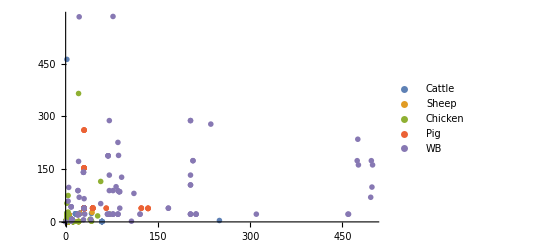
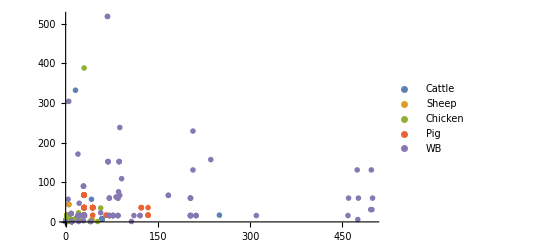
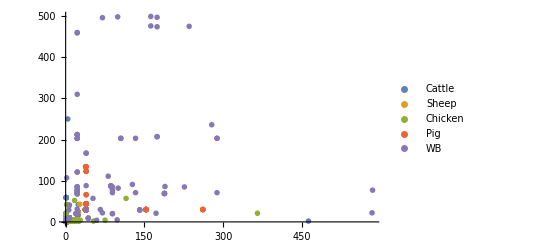
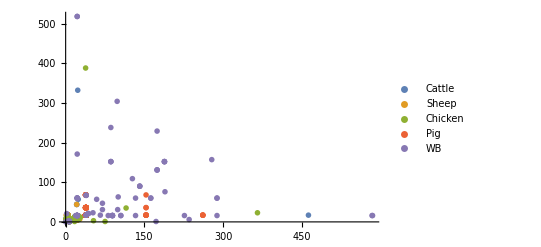
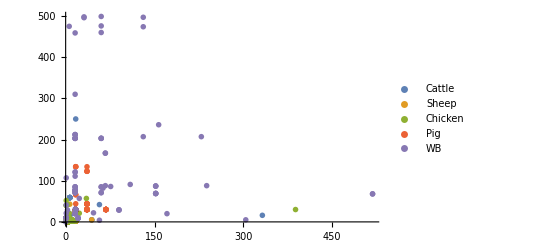
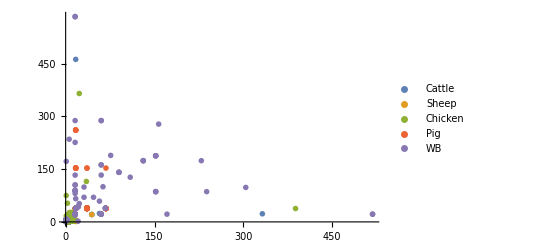
gene 3 | -Graphics- | -Graphics-
-Graphics- | gene 2 | -Graphics-
-Graphics- | -Graphics- | gene 7

```mathematica
ScatterPlotMatrix[dataSources[[All,2;;8]],featurename,{3,2,7},dataSources[[All,1]]]
```

## Task 10

To train a classifier with the source isolates and test its performance, you will need to define training and test datasets from the dataSources list.

In dataSources, there are some isolates that are identical (i.e. they share the same features). See, for instance the first 10 elements of the Tally counts in dataSources:

```mathematica
Take[Tally[dataSources],10]
```

{{{Cattle,2,1,5,3,725,1,5},2},{{Cattle,1,2,3,4,5,9,3},21},{{Cattle,19,24,23,20,26,16,15},8},{{Cattle,2,1,1,3,2,1,5},10},{{Cattle,1,4,2,2,6,3,17},18},{{Cattle,9,2,4,62,4,5,6},7},{{Cattle,1,1,59,2,10,5,7},5},{{Cattle,1,462,2,2,6,3,17},1},{{Cattle,2,1,5,3,2,1,5},19},{{Cattle,1,3,6,4,3,3,3},4}}

For instance, there are 8 isolates from cattle with the genotype {Cattle,19,24,23,20,26,16,15}.

Due to the repeated genotypes, to define training and test datasets you should select element numbers in lists. For instance, to select 75% of the isolates from dataSources at random to define the training dataset, we proceed as follows:

First calculate the number of isolates corresponding to 75% of the total in dataSources. Let us refer to this quantity as ntrain.

```mathematica
673*0.75
```

504.75

```mathematica
ftrain=0.75;
ntrain=Round[ftrain Length[dataSources]]
```

505

Choose ntrain indices from the set {1,2,...,Length[dataSources]} at random for the training data. Let us refer to the resulting set of indices as indexTraindata.

```mathematica
{1,2,3,4...,673}
```

{1,2,3,(4)...,673}

```mathematica
indexTraindata=RandomSample[Range[Length[dataSources]],ntrain];
```

```mathematica
Length[indexTraindata]
```

505

Use the Complement function to define indices to be chosen from the original set to define the test dataset. Hint: This is the complement between a set of all the indices in dataSources and in indesTraindata.

```mathematica
indexTestdata=Complement[Range[Length[dataSources]],indexTraindata];
```

Check that the intersection between indexTraindata and indexTestdata is null.

Use the indices indexTraindata and indexTestdata to define lists for training and testing from dataSources. I will refer to these as traindata and testdata, respectively.

Check that traindata and testdata look as you would expect (e.g. they have the right dimensions)

### Answer

The intersection is null:

```mathematica
Intersection[indexTraindata,indexTestdata]
```

{}

The training and test lists:

```mathematica
traindata=dataSources[[indexTraindata]];
```

```mathematica
testdata=dataSources[[indexTestdata]];
```

We do few tests to see if these lists look as we would expect:

```mathematica
Take[traindata,10]
```

{{Chicken,4,7,10,4,42,7,1},{Sheep,1,2,3,4,5,9,3},{Pig,33,38,30,82,118,43,17},{WB,64,22,85,98,652,270,60},{Cattle,33,39,30,82,104,56,17},{Pig,33,39,30,82,104,117,17},{Pig,33,38,30,174,104,43,17},{WB,64,22,31,100,134,103,16},{Sheep,1,2,3,4,5,9,3},{Cattle,1,4,2,2,6,3,17}}

```mathematica
Take[testdata,10]
```

{{Cattle,2,1,1,3,2,1,5},{Cattle,1,1,59,2,10,5,7},{Cattle,2,1,12,88,2,1,5},{Cattle,2,1,1,3,2,1,5},{Cattle,19,24,23,20,26,16,15},{Cattle,1,2,3,4,5,9,3},{Cattle,1,1,59,2,10,5,7},{Cattle,33,39,30,82,104,56,17},{Cattle,1,4,2,2,6,3,17},{Cattle,33,39,30,82,104,56,17}}

```mathematica
Length[traindata]
```

505

```mathematica
Length[testdata]
```

168

## Task 11

Use the Classify function with traindata to train a classifier for Campylobacter sources.

### Answer

```mathematica
cOne=Classify[traindata[[All,2;;8]]-> traindata[[All,1]]]
```

ClassifierFunction[…]

## Task 12

What classification method did Mathematica choose as the most accurate?

Display the learning curve for the classifier. In particular, look at the learning curve of different methods tested by Mathematica. Comment on the differences between methods.

### Answer

To start with, it is useful to look at the list of properties of the classifier:

```mathematica
Information[cOne,"Properties"]
```

{Accuracy,BatchEvaluationSpeed,BatchEvaluationTime,BoostingMethod,Classes,ClassNumber,ClassPriors,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,L1Regularization,L2Regularization,LeafSize,LearningCurve,LearningRate,LeavesNumber,MaxDepth,MaxTrainingMemory,MaxTrainingRounds,MeanCrossEntropy,Method,MethodDescription,MethodOption,PerformanceGoal,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

The chosen method is

```mathematica
Information[cOne,"Method"]
```

GradientBoostedTrees

This is also displayed in the classifier function obtained in the previous task.

The learning curve for the chosen method and all methods can be seen as:

```mathematica
Information[cOne,"LearningCurve"]
```

The accuracy of the chosen method in this case is close to other methods and it is likely that the best method depends on the specific random selection of isolates for the training dataset.

## Task 13

Use the testdata list to obtain a ClassifierMeasurements object to test the performance of the classifier trained above.

### Answer

```mathematica
cmOne=ClassifierMeasurements[cOne,Table[testdata[[i,2;;8]]-> testdata[[i,1]],{i,1,Length[testdata]}]]
```

ClassifierMeasurementsObject[…]

## Task 14

Using the ClassifierMeasurements object obtained in the previous task, look at the following:

Accuracy of the classifier

Confusion matrix. Comment on the results (e.g. which are the less confused classes? which are the most confused classes? Is confusion symmetric among classes? Can confusion be understood in terms of your exploration of the data in previous tasks in terms of scatter plots?).

Calculate the true positive rate (TPR) for all the classes and plot the results in a bar chart with a bar for the TPR for each class (food reservoir). Comment on the meaning of TPR in this problem and discuss the results.

### Answer

To start with, it is useful to list all the properties of the classifier

```mathematica
cmOne["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeNumber,FalseNegativeRate,FalsePositiveExamples,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictiveValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TrueNegativeNumber,TruePositiveExamples,TruePositiveNumber,WorstClassifiedExamples}

The specific value of the accuracy and any other measures of performance for the classifier will depend a bit on the particular training and test datasets you have chosen at random.

Accuracy is typically not very high for this classification problem:

```mathematica
cmOne["Accuracy"]
```

0.672619

Typically, the confusion matrix shows that sheep and cattle isolates are the most confused and confusion seems to be reasonably symmetric among these two sources. Pig isolates are typically the most accurately attributed isolates, followed by wild bird isolates. These trends agree with the qualitative analysis based on the scatter plots studied above. For instance, we saw that cattle and sheep isolates are closer to each other in the feature space. This explains the larger confusion.

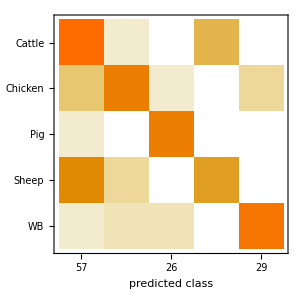

```mathematica
cmOne["ConfusionMatrixPlot"]
```

The true positive rate gives the proportion of isolates in the training dataset that are correctly attributed to their source.

One can calculate TPRs for all the classes as follows:

```mathematica
TPROne=cmOne["TruePositiveRate"]
```

<|Cattle→0.692308,Chicken→0.638889,Pig→0.958333,Sheep→0.384615,WB→0.833333|>

The bar chart of TPR can be plot as follows:

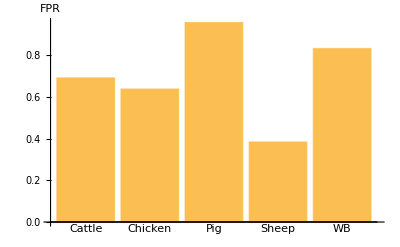

```mathematica
BarChart[Values[TPROne],ChartLabels->Keys[TPROne],AxesLabel->"FPR"]
```

## Task 15

Look at the worst and best classified examples. Is there a clear trend that would allow us to conclude that the classification of isolates from some reservoirs is typically less accurate than other? To have a more complete view on this, you might find useful to create a table for sorted probabilities for each prediction.

### Answer

The specific results will depend on the particular random lists for  used for traindata and testdata. However, I found that some wild bird isolates are typically always among the worst classified and some pig isolates are among the best classified. A general trend, however, is not clear.

```mathematica
cmOne["WorstClassifiedExamples"]
```

{{0,0,0,0,0,0,0}→WB,{2,59,4,48,131,24,57}→WB,{33,39,30,82,113,44,17}→Pig,{33,39,30,82,113,47,17}→Cattle,{10,27,43,19,6,18,7}→Sheep,{19,24,23,20,26,16,15}→Sheep,{33,39,30,82,711,56,17}→Sheep,{33,38,30,82,104,43,388}→Chicken,{33,39,30,82,104,56,17}→Chicken,{2,1,1,3,2,1,3}→Chicken}

```mathematica
cmOne["BestClassifiedExamples"]
```

{{104,7,10,4,1,7,1}→Chicken,{7,17,2,15,23,3,12}→Chicken,{24,2,2,2,10,3,3}→Chicken,{24,2,2,2,10,3,3}→Chicken,{24,2,2,2,10,3,3}→Chicken,{2,1,1,3,2,1,3}→Sheep,{33,39,30,82,104,43,17}→Pig,{33,39,66,82,104,44,17}→Pig,{33,38,30,82,104,43,17}→Pig,{33,38,30,82,104,43,17}→Pig}

```mathematica
TableForm[SortBy[Transpose[{testdata[[All,1]],cmOne["Probabilities"]}],Last]];
```

## Task 16

Now that we have checked that a classifier for Campylobacter with the current dataset is reasonably accurate, we are in a position to attribute human isolates to sources. We expect that the accuracy of a classifier would increase with the number of isolates used to train it. Accordingly, it makes sense to use all the isolates in dataSources to train a new classifier to attribute human isolates.

Use all the source isolates in dataSources to train a new classifier.

### Answer

```mathematica
cAllSourcesOne=Classify[Table[dataSources[[i,2;;8]]-> dataSources[[i,1]],{i,1,Length[dataSources]}]]
```

ClassifierFunction[…]

## Task 17

Use the classifier found in Task 16 to classify the human isolates stored in dataHuman. Assign the results to a variable named as attribHuman.

### Answer

```mathematica
attribHumanOne=cAllSourcesOne[dataHuman[[All,2;;8]]];
```

## Task 18

Count the number of human isolates attributed to each source. Represent the fraction of human isolates attributed to each source in a bar chart. Describe the results in words.

### Answer

```mathematica
attribNumbersOne=Tally[attribHumanOne]
```

{{Pig,17},{Chicken,320},{Sheep,103},{Cattle,45},{WB,15}}

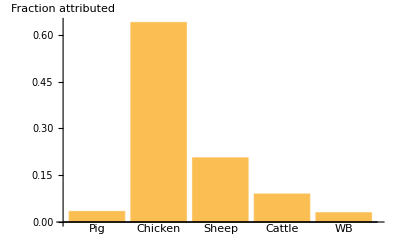

```mathematica
BarChart[attribNumbersOne[[All,2]]/Total[attribNumbersOne[[All,2]]],ChartLabels->attribNumbersOne[[All,1]],AxesLabel->"Fraction attributed"]
```

Most of human isolates are attributed to chicken, followed by sheep. This suggests that chicken is the main Campylobacter reservoir affecting humans.

## Option 2: Training A Classifier Function Mitigating Bias

## Task 1

Download the dataset Campylobacter_MLST.csv from MyAberdeen

Import the data and assign it to a variable (e.g. data)

### Answer

```mathematica
(*Paco's import*)
initialdata=SemanticImport["~/Teaching/MSc_Data_Science/Data/Campylobacter/Campylobacter_MLST.csv"];
```

```mathematica
(*Luke's import*)
SetDirectory[NotebookDirectory[]]
initialdata=SemanticImport["Campylobacter_MLST.csv"];
```

Lets assign column headers to the data

```mathematica
data=initialData[All,<|"classification"->1,"geneOne"->2,"geneTwo"->3,"geneThree"->4,"geneFour"->5,"geneFive"->6,"geneSix"->7,"geneSeven"->8|>];
```

## Task 2

Examine the format of the dataset. For instance, use the function Take to see the 10 first instances and look at the dimensions of the dataset. As you will see, data is a list of lists. It can be thought as a table consisting of 8 columns and 1173 rows. The first column gives the category of each isolate and each row corresponds to a different isolate.

### Answer

```mathematica
data[[;;10,;;]];
```

```mathematica
Dimensions@data
```

{1173,8}

## Task 3

Look at the name of different categories in the dataset which are given in the first column for each instance (isolate). This can be done by DeleteDuplicates.

### Answer

```mathematica
DeleteDuplicates@data[[;;,1]]
```

## Task 4

Since the isolates from food reservoirs are assumed to be the sources of human isolates, it makes sense to split the list data into two lists, one corresponding to human isolates and another for isolates from food reservoirs.  The resulting lists should have the same format (e.g. same number of columns) as data. More explicitly:

Create a sublist from data for human isolates. Refer to it as dataHuman. (Hint: use the function Position of “Human” in the first column of data to select the rows of data corresponding to humans).

Create a list containing the data for food reservoirs only. Refer to the new list as dataSources. Hint: Use the complement of the rows corresponding to humans.

As usual when defining new lists or variables, check that they look like you expect them to look.

### Answer

```mathematica
dataHuman=data[Select[#classification=="Human"&]];
dataSources=data[Select[#classification!="Human"&]];
```

Checking Dimensions

```mathematica
Dimensions@dataHuman
Dimensions@dataSources
```

{500,8}

{673,8}

## Task 5

Use dataSources to define a list named sourcenames containing the name of the sources. This will be useful to explore the data below. Note that isolates from wild birds are labeled as WB.

### Answer

```mathematica
sourcenames=DeleteDuplicates[dataSources[[;;,1]]]//Normal
```

{Cattle,Sheep,Chicken,Pig,WB}

## Task 6

In the forthcoming analysis, it will be useful to have a list with the name of features (genes). For the purposes of this practical, you can refer to the genes as “gene 1”, “gene 2”,... “gene 7”

```mathematica
featurename={"gene 1","gene 2","gene 3","gene 4","gene 5","gene 6","gene 7"};
```

## Task 7

Separate the instances in dataSources by source. I will refer to the new list as bySources. In order to achieve this task, you may want to go back to the Iris flowers classification example where a similar task was done.

### Answer

```mathematica
SortData[list_List]:=
Module[{test,datalength,sorteddata},
test=GroupBy[list[[;;,;;]],First];
datalength=Min[Table[Length[test[[i]]],{i,Length[test]}]];
sorteddata=Flatten[Table[{Take[test[[i]],datalength]},{i,Length[Keys[test]]}],2]];
bySources=Reverse[GroupBy[SortData[Values@dataSources//Normal],First]];
```

```mathematica
bySources[[1]]
```

{{WB,35,43,9,5,121,46,21},{WB,26,43,9,101,8,46,21},{WB,33,39,30,79,104,35,17},{WB,258,174,207,193,336,590,131},{WB,64,22,85,98,134,101,16},{WB,64,22,203,100,134,591,16},{WB,64,22,459,100,134,94,16},{WB,18,22,77,98,122,101,16},{WB,18,22,77,98,122,101,16},{WB,76,22,460,100,751,592,60},{WB,64,133,203,142,134,160,60},{WB,64,22,121,100,752,3,16},{WB,80,89,71,98,652,594,16},{WB,64,105,203,100,134,94,16},{WB,64,89,20,98,134,593,16},{WB,64,105,203,100,134,94,16},{WB,64,133,71,98,652,94,16},{WB,64,22,31,100,134,103,16},{WB,64,288,71,98,652,94,16},{WB,64,22,203,100,134,258,16},{WB,64,226,85,100,134,54,16},{WB,258,174,474,193,753,595,131},{WB,18,235,475,18,134,285,6},{WB,18,22,77,98,122,101,16},{WB,64,19,20,98,754,101,16},{WB,64,288,203,189,134,94,60},{WB,64,22,121,100,134,270,16},{WB,64,22,85,98,652,270,60},{WB,64,89,20,77,122,103,16},{WB,64,22,203,100,134,103,16},{WB,18,89,77,98,122,101,16},{WB,64,22,20,100,134,101,171},{WB,258,174,207,193,336,314,229},{WB,64,22,212,97,122,301,16},{WB,64,22,85,98,652,270,60},{WB,396,162,476,100,194,101,60},{WB,270,98,5,397,511,596,304},{WB,37,52,57,26,380,29,23},{WB,76,70,496,104,116,109,31},{WB,64,89,85,189,134,101,16},{WB,64,583,22,111,122,303,16},{WB,64,288,203,189,134,187,60},{WB,258,174,497,193,574,615,131},{WB,64,22,310,100,134,94,16},{WB,64,22,212,97,122,301,16},{WB,27,99,498,104,774,285,31},{WB,64,22,71,189,134,118,60},{WB,64,22,212,97,122,301,16},{WB,64,22,68,100,134,593,518},{WB,64,22,68,100,134,593,518},{WB,64,22,71,100,134,187,60},{WB,64,584,77,100,138,101,16},{WB,64,162,499,100,194,101,60},{WB,81,86,87,113,270,238,152},{WB,33,39,167,113,265,43,67},{WB,135,188,69,113,276,43,152},{WB,135,188,69,113,276,43,152},{WB,86,86,88,245,288,129,238},{WB,33,39,167,113,265,43,67},{WB,210,278,236,318,406,329,157},{WB,81,86,87,113,270,238,152},{WB,33,39,88,113,265,43,67},{WB,0,0,0,0,0,0,0},{WB,86,189,86,259,287,236,76},{WB,135,188,69,113,276,43,152},{WB,33,39,30,82,113,44,17},{WB,136,188,69,113,270,43,152},{WB,33,39,30,82,104,56,17},{WB,33,66,30,192,189,44,17},{WB,81,86,87,113,270,238,152},{WB,33,39,30,82,113,47,17},{WB,4,7,10,4,1,7,1},{WB,4,7,10,4,1,7,1},{WB,4,7,10,4,1,7,1},{WB,4,7,10,4,1,7,1},{WB,18,22,22,18,194,269,16},{WB,10,2,107,137,120,76,1},{WB,99,127,91,508,184,148,109},{WB,4,7,10,4,1,7,1},{WB,35,43,9,5,121,46,21},{WB,26,2,9,51,8,46,21},{WB,1,6,29,2,40,32,3},{WB,2,59,4,48,131,24,57},{WB,4,7,10,4,42,51,1},{WB,4,7,10,4,1,7,1},{WB,18,100,82,24,138,116,63},{WB,4,7,41,4,42,7,1},{WB,18,81,111,143,134,153,16},{WB,7,172,21,49,125,224,1},{WB,61,70,22,18,2,74,47},{WB,84,141,29,28,526,465,90},{WB,84,141,29,28,526,465,90},{WB,84,141,29,28,526,465,90}}

## Task 8

The goal of the classifier to be trained in this practical will be to classify unseen isolates into food reservoirs. In order for classification to be accurate, we need a reasonable separation between different reservoirs in the feature space. The feature space in this case consists of 7 dimensions (each isolate is represented by a point in this space and its coordinates are the values taken by its 7 genes). 

Since the dimension of the feature space is larger than 3, it is difficult to visualise at once on a 2D screen. 

One possible way to do a preliminary exploration is to plot the alleles for pairs of genes (pairs of features) and pairs of sources. This can be done using the following scatterplot:

```mathematica
bySources[[1]][[1]]
```

{WB,35,43,9,5,121,46,21}

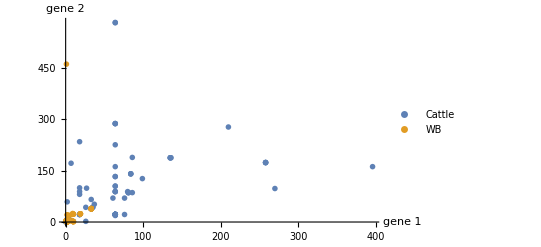

```mathematica
f1=1;
f2=2;
source1=1;
source2=5;
ListPlot[{bySources[[source1]][[All,{f1+1,f2+1}]],bySources[[source2]][[All,{f1+1,f2+1}]]},AxesLabel->featurename[[{f1,f2}]],PlotLegends->sourcenames[[{source1,source2}]],PlotMarkers->{"OpenMarkers", Medium},PlotRange->All]
```

Here, f1 and f2 correspond to features (genes). source1 and source2 correspond to two reservoirs.

In order to compare pairs of reservoirs, I suggest you proceed as follows:

Make sure you understand how the plot is made.

Systematically compare the scatterplot for pairs of sources and pairs of genes. The comparison between sources in this case is not as clear as the comparison between species in the Iris flowers problem. However, we can extract some preliminary conclusions. Which sources do you think are more different from each other? These are the ones that the classifier you will train later should identify more accurately.

### Answer

Although it is not easy to identify clear trends in the data, one can observe the following:

WB isolates are the ones that cover a larger part of the feature space. They seem to be quite different to other isolates.

Pig isolates also cover a large region in the feature space and do not overlap much with other sources.

The point clouds for cattle and sheep seem to overlap more than those for any other sources.

The point clouds for chicken does not spread over a region as wide as pig and WB but they seem to be reasonably separated from the clouds of other sources.

You may find useful to use a scatterplot with dynamical ranges as follows (make sure you understand how this is built):

```mathematica
f1=1;
f2=2;
Manipulate[ListPlot[Table[bySources[[i]][[All,{f1+1,f2+1}]],{i,1,Length[sourcenames]}],PlotLegends->sourcenames,PlotMarkers->{"OpenMarkers", Medium},PlotRange->{{0,x},{0,y}}],{x,10,800},{y,10,800}]
```

## Task 9

In order to further analyse the data and try to confirm some of your conclusions in the previous task, you can use a a scatter plot matrix using the function ScatterPlotMatrix defined in lectures for the Iris flower classification problem. In order to reduce the complexity of the scatter plot matrix, you may want to plot a reduced number of features (genes) at once.

### Answer

One can define a function to do scatter plot matrix plots automatically. The inputs for the function are as follows:

values: matrix with values for all features
names: names of the features
vfeatures: vector with the feature number to be plotted 
vclass: vector with class of each instance

```mathematica
ScatterPlotMatrix[values0_,names0_,vfeatures0_,vclass0_]:=Module[{values=values0,names=names0,vf=vfeatures0,vc=vclass0,classes,pos},
classes=DeleteDuplicates[vc];
pos=Table[Flatten[Position[vc,classes[[i]]]],{i,1,Length[classes]}];
Table[If[i==j,names[[i]],ListPlot[Table[Transpose[{values[[pos[[ic]],i]],values[[pos[[ic]],j]]}],{ic,1,Length[classes]}],PlotMarkers->{"OpenMarkers", Small},PlotLegends->DeleteDuplicates[vclass0],PlotRange->All]],{i,vf},{j,vf}]//Grid
]
```

For instance, the scatter plots for the first three genes look like:

```mathematica
ScatterPlotMatrix[Values@dataSources[[;;,2;;8]]//Normal,featurename,Range[7],dataSources[[;;,1]]//Normal];
```

## Task 10

To train a classifier with the source isolates and test its performance, you will need to define training and test datasets from the dataSources list.

### Answer

This function splits the data evenly between the classifications that are used by the target variable

#### Sort Function

```mathematica
SortData[list_List]:=
Module[{test,datalength,sorteddata},
test=GroupBy[list[[;;,;;]],First];
datalength=Min[Table[Length[test[[i]]],{i,Length[test]}]];
sorteddata=Flatten[Table[{Take[test[[i]],datalength]},{i,Length[Keys[test]]}],2]];
```

#### Sorting The Data

Grouping the data by the target variable values

```mathematica
bySources=Reverse[GroupBy[SortData[Values@dataSources//Normal],First]];
```

```mathematica
Keys@bySources
```

{WB,Pig,Chicken,Sheep,Cattle}

```mathematica
α=Length[bySources[[1]]]
```

93

Now we need to split this data in terms of training and test data.
Creating a variable to hold 75% of the data. The data set isn’t that large, so it will be divided 80/20 between training and test data

```mathematica
trainN=Floor[0.75*α]
```

69

Given a list (the first argument), the TakeDrop function[]  selects the first n elements, (second argument) and returns it as the first sublist in a list object.
  The remainder is placed in the second sublist. These two sublists can be then individually named as two separate objects. By adding the RandomSample[] function, a random selection of rows of similar size , n, is taken as first sublist. and the complement is stored in the second sublist

```mathematica
dataTrain=Flatten[Table[Table[TakeDrop[RandomSample@bySources[[i]],trainN],{i,1,Length[Keys@bySources]}][[j]][[1]],{j,Length[Keys@bySources]}],1];
dataTest=Flatten[Table[Table[TakeDrop[RandomSample@bySources[[i]],trainN],{i,1,Length[Keys@bySources]}][[j]][[2]],{j,Length[Keys@bySources]}],1];
```

```mathematica
Dimensions[dataTrain]
Dimensions[dataTest]
```

{345,8}

{120,8}

Create variables to separately hold the feature variables and the target variables for each of the following training and test sets.

```mathematica
xTrain=dataTrain[[All,2;;8]];
yTrain=dataTrain[[All,1]];
xTest=dataTest[[All,2;;8]];
yTest=dataTest[[All,1]];
```

Lets take  a look to see if the class distribution is equal

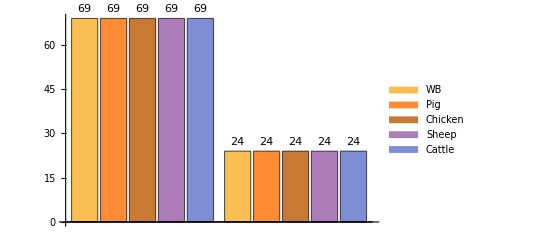

```mathematica
BarChart[{Counts@yTrain,Counts@yTest},ChartLegends->Automatic,LabelingFunction->Above]
```

Mapping the Classification label to the training and test data

```mathematica
trainDataTwo=Table[xTrain[[i]]->yTrain[[i]],{i,Length[yTrain]}]//N;
testDataTwo=Table[xTest[[i]]->yTest[[i]],{i,Length[yTest]}]//N;
```

## Task 11

Use the Classify function with traindata to train a classifier for Campylobacter sources.

### Answer

```mathematica
cTwo=Classify[trainDataTwo]
```

ClassifierFunction[…]

## Task 12

What classification method did Mathematica choose as the most accurate?

Display the learning curve for the classifier. In particular, look at the learning curve of different methods tested by Mathematica.

### Answer

To start with, it is useful to look at the list of properties of the classifier:

We can use manipulate to scroll through the properties

```mathematica
Manipulate[Information[cTwo,prop],{prop,Information[cTwo,"Properties"]},SaveDefinitions->True]
```

The accuracy of the chosen method in this case is close to other methods and it is likely that the best method depends on the specific random selection of isolates for the training dataset.

## Task 13

Use the testdata list to obtain a ClassifierMeasurements object to test the performance of the classifier trained above.

### Answer

```mathematica
cmTwo=ClassifierMeasurements[cTwo,testDataTwo]
```

ClassifierMeasurementsObject[…]

## Task 14

Using the ClassifierMeasurements object obtained in the previous task, look at the following:

Accuracy of the classifier

Confusion matrix. Comment on the results (e.g. which are the less confused classes? which are the most confused classes? Is confusion symmetric among classes? Can confusion be understood in terms of your exploration of the data in previous tasks in terms of scatter plots?).

Calculate the true positive rate (TPR) for all the classes and plot the results in a bar chart with a bar for the TPR for each class (food reservoir). Comment on the meaning of TPR in this problem and discuss the results. Hint: Since the TPR given by the ClassifierMeasurements object results in an association, you may find useful the Keys and Values commands to plot the bar chart with labels for each bar.

### Answer

The specific value of the accuracy and any other measures of performance for the classifier will depend a bit on the particular training and test datasets you have chosen at random.

Accuracy is typically not very high for this classification problem:

We can use Manipulate to scroll through the object

```mathematica
Manipulate[cmTwo[prop],{prop,cmTwo["Properties"]},SaveDefinitions->True]
```

Typically, the confusion matrix shows that sheep and cattle isolates are the most confused and confusion seems to be reasonably symmetric among these two sources. Pig isolates are typically the most accurately attributed isolates, followed by wild bird isolates. These trends agree with the qualitative analysis based on the scatter plots studied above. For instance, we saw that cattle and sheep isolates are closer to each other in the feature space. This explains the larger confusion.

The true positive rate gives the proportion of isolates in the training dataset that are correctly attributed to their source.

One can calculate TPRs for all the classes as follows:

```mathematica
TPRTwo=cmTwo["TruePositiveRate"]
```

<|Cattle→0.666667,Chicken→0.75,Pig→0.916667,Sheep→0.291667,WB→0.625|>

The bar chart of TPR can be plot as follows:

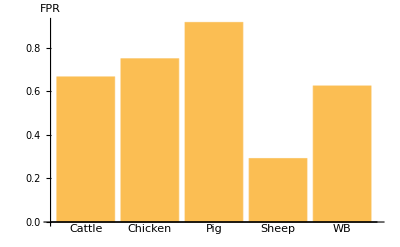

```mathematica
BarChart[Values[TPRTwo],ChartLabels->Keys[TPRTwo],AxesLabel->"FPR"]
```

## Task 15

Look at the worst and best classified examples. Is there a clear trend that would allow us to conclude that the classification of isolates from some reservoirs is typically less accurate than other? To have a more complete view on this, you might find useful to create a table for sorted probabilities for each prediction (this was done for the Iris flowers problem in lectures).

### Answer

The specific results will depend on the particular random lists for  used for traindata and testdata. However, I found that some wild bird isolates are typically always among the worst classified and some pig isolates are among the best classified. A general trend, however, is not clear.

```mathematica
cmTwo["WorstClassifiedExamples"]
```

{{26.,2.,9.,51.,8.,46.,21.}→WB,{33.,39.,30.,82.,104.,56.,17.}→WB,{33.,39.,30.,82.,104.,56.,17.}→Chicken,{7.,21.,5.,62.,4.,61.,44.}→Sheep,{2.,1.,12.,3.,2.,1.,5.}→Cattle,{2.,1.,1.,3.,2.,1.,5.}→Cattle,{2.,4.,1.,2.,7.,1.,5.}→Sheep,{2.,4.,1.,2.,7.,1.,5.}→Cattle,{9.,17.,52.,10.,10.,3.,1.}→Chicken,{2.,1.,5.,3.,2.,1.,5.}→Chicken}

```mathematica
cmTwo["BestClassifiedExamples"]
```

{{7.,17.,2.,3.,23.,3.,12.}→Chicken,{8.,10.,2.,2.,11.,12.,6.}→Chicken,{24.,2.,2.,2.,10.,3.,3.}→Chicken,{8.,10.,2.,2.,11.,12.,6.}→Chicken,{2.,4.,1.,2.,7.,1.,5.}→Chicken,{2.,4.,1.,2.,7.,1.,5.}→Chicken,{24.,2.,2.,2.,10.,3.,3.}→Chicken,{1.,2.,3.,4.,5.,9.,3.}→Cattle,{1.,2.,3.,4.,5.,9.,3.}→Cattle,{84.,141.,29.,28.,526.,465.,90.}→WB}

```mathematica
Table[{testDataTwo[[i]],cmTwo["Probabilities"][[i]]},{i,Length[testDataTwo]}]//TableForm;
```

## Task 16

Now that we have checked that a classifier for Campylobacter with the current dataset is reasonably accurate, we are in a position to attribute human isolates to sources. We expect that the accuracy of a classifier would increase with the number of isolates used to train it. Accordingly, it makes sense to use all the isolates in dataSources to train a new classifier to attribute human isolates.

Use all the source isolates in dataSources to train a new classifier.

```mathematica
cAllSourcesTwo=Classify[Table[dataSources[[i,2;;8]]-> dataSources[[i,1]],{i,1,Length[dataSources]}]]
```

ClassifierFunction[…]

## Task 17

Use the classifier found about to classify the human isolates stored in dataHuman. Assign the results to a variable named as attribHuman.

### Answer

```mathematica
attribHumanTwo=cAllSourcesTwo[dataHuman[[;;,2;;8]]];
```

## Task 18

Apply the Tally function to attribHuman to count the number of human isolates attributed to each source. Represent the fraction of human isolates attributed to each source in a bar chart. Describe the results in words.

### Answer

```mathematica
attribNumbersTwo=Tally[attribHumanTwo]
```

{{Pig,17},{Chicken,320},{Sheep,103},{Cattle,45},{WB,15}}

```mathematica
BarChart[attribNumbersTwo[[All,2]]/Total[attribNumbersTwo[[All,2]]],ChartLabels->attribNumbersTwo[[All,1]],AxesLabel->"Fraction attributed"]
```

-Graphics-